```mathematica
f[n_]:=(nums=Range[1,6];p=ConstantArray[1,6];m=1;
While[m<n, 
numsold=nums;pold=p;
nums=Range[1,Length[numsold]+6];
p=ConstantArray[0,Length[nums]];
For[i=1, i≤Length[numsold],i++,
For[j=1,j≤6,j++,
p[[i+j]]+=pold[[i]]
]
]
;m++];
pfinal=p/Total[p];
Transpose[{nums,pfinal}])
fscaled[n_]:=(nums=Range[1,6];p=ConstantArray[1,6];m=1;
While[m<n, 
numsold=nums;pold=p;
nums=Range[1,Length[numsold]+6];
p=ConstantArray[0,Length[nums]];
For[i=1, i≤Length[numsold],i++,
For[j=1,j≤6,j++,
p[[i+j]]+=pold[[i]]
]
]
;m++];
pnew=p/Total[p];
max=Max[pnew];
pfinal = pnew/max;
Transpose[{nums/Length[nums],pfinal}])
```

### Part a)

1 | 0
2 | 1/36
3 | 1/18
4 | 1/12
5 | 1/9
6 | 5/36
7 | 1/6
8 | 5/36
9 | 1/9
10 | 1/12
11 | 1/18
12 | 1/36

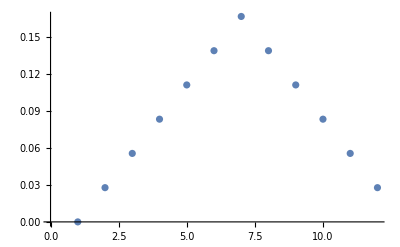

```mathematica
f[2]//TableForm
ListPlot[f[2]]
```

### Part b)

1 | 0
2 | 0
3 | 1/216
4 | 1/72
5 | 1/36
6 | 5/108
7 | 5/72
8 | 7/72
9 | 25/216
10 | 1/8
11 | 1/8
12 | 25/216
13 | 7/72
14 | 5/72
15 | 5/108
16 | 1/36
17 | 1/72
18 | 1/216

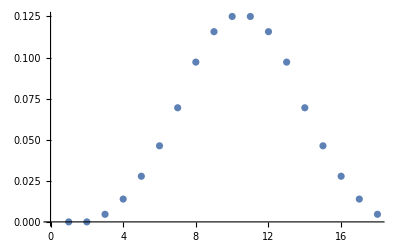

```mathematica
f[3]//TableForm
ListPlot[f[3]]
```

### Part c)

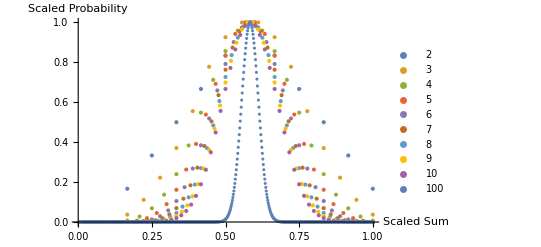

```mathematica
Show[ListPlot[Table[fscaled[x],{x,2,10,1}],PlotLegends->Range[2,10,1],PlotRange->All,AxesLabel->{"Scaled Sum","Scaled Probability"}],ListPlot[fscaled[100],PlotLegends->{100}]]
```